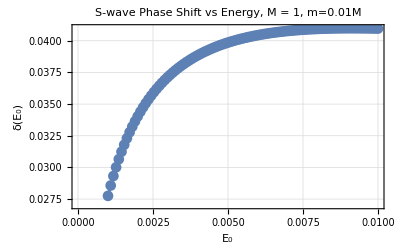

```mathematica
(*---PARAMETERS---*)
M=1;                (* Mass of Nucleon*)
m=0.1*M;               (*Pion mass*)
α=0.01;              (*Depth of Yukawa potential*)
r0=10^-6;          (*Small value near r=0 for boundary condition*)

EMin = m^2/10;
EMax = m^2; 
ESpacing = (EMax-EMin)/100(*0.01*m^2*);
k0=Sqrt[EMax*M];
λ = 2*Pi/Abs[k0]; (* De Broglie Wavelength*)
rMax=20*λ;           (*Max radius for numerical integration, ensures asymptotic behavior by being much larger than λ*)
fitStart=0.8*rMax;       (*Start of asymptotic region*)
fitEnd=rMax;         (*End of asymptotic region*)
fitSpacing = rMax/100;    (* Interval spacing in asymptotic region*)

(*---Yukawa Potential---*)
V[r_]:=-α*Exp[-m*r]/r;

(*---Phase Shift Extractor---*)
ClearAll[extractPhaseShift]

extractPhaseShift[E0_?Positive,M_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=Sqrt[M*E0];
(*Numerical solution to Schrödinger equation*)sol=NDSolve[{u''[r]==M*(V[r]-E0) u[r],u[r0]==r0,u'[r0]==1},u,{r,r0,rMax},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,fitStart,fitEnd,fitSpacing}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r+δ],{{A,1},{δ,0}},r];
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi]]

(*---Phase Shift Curve Generator---*)
energyRange=Range[EMin,EMax,ESpacing];  (*Energies to test*)

phaseShiftData=Table[{E0,extractPhaseShift[E0,M]},{E0,energyRange}];

(*---Plot the phase shift vs energy---*)
ListLinePlot[phaseShiftData,PlotMarkers->Automatic,AxesLabel->{"E₀","δ(E₀)"},PlotLabel->Row[{"S-wave Phase Shift vs Energy, M = ",M,", m=0.01M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed"]
```